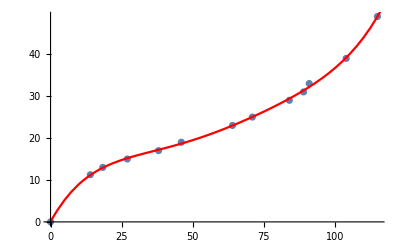

0.028248192731641895 + 1.2351675034207708*(ball_dist) - 0.04034545106528184*(ball_dist)**2 + 0.0007162981851352722*(ball_dist)**3 - 5.9109828451806266e-6*(ball_dist)**4 + 1.913654033502916e-8*(ball_dist)**5

```mathematica
(*Input format is {dist to edge of bot, pixel distance}*)
data={{-9,0},{2.25,14},{4,18.38},{6,27},{8,38},{10,46},{14,64},{16,71},{20,84},{22,89},{24,91},{30,104},{40,115}};
data[[All,1]]+=9; data=Reverse/@data;
n=5; (*what order polynomial to fit*)
bestFit=Fit[data,Table[x^k,{k,0,n}],x];
Show[ListPlot[data,PlotRange->All],Plot[{bestFit},{x,0,120},PlotStyle->Red]]
bestFit/.{x->ball_dist};
pythonStr=ToString[bestFit/.{x->ball_dist},InputForm];
pythonStr=StringReplace[pythonStr,"*^"->"e"];
pythonStr=StringReplace[pythonStr,"^"->"**"];
pythonStr
```